```mathematica
$Assumptions = {Vg ∈ Reals, V0 ∈ Reals, κ ∈ Reals, a ∈ Reals, n ∈ Integers, Subscript[k, F] ∈ Reals, q ∈ Reals, q > 0}
```

{Vg∈ℝ,V0∈ℝ,κ∈ℝ,a∈ℝ,n∈ℤ,k_F∈ℝ,q∈ℝ,q>0}

# Preliminaries

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
FullSimplify[ω^2 * (x + I y) + Conjugate[ω^2] * (x - I y)]
```

-x+√3 y

```mathematica
αF=V0 * (Sqrt[3] I a n κ^2 Subscript[k, F]^2)/(8 (1 + κ^2))
```

(ⅈ √3 a n V0 κ^2 k_F^2)/(8 (1+κ^2))

```mathematica
ΔF = - (V0/3) (π Subscript[k, F]^2)
```

-1/3 π V0 k_F^2

```mathematica
αH=-(Vg/3) (Subscript[k, F]^2/(8 (1 + κ^2)^3)) (1 + κ^2 ω^n) (4 π κ (ω^n - 1) - 3 Sqrt[3] I a n κ^2 (1 + κ^2))
```

-(Vg (1+(ⅇ^((2 ⅈ π)/3))^n κ^2) (4 (-1+(ⅇ^((2 ⅈ π)/3))^n) π κ-3 ⅈ √3 a n κ^2 (1+κ^2)) k_F^2)/(24 (1+κ^2)^3)

```mathematica
ΔH = (Vg/3) ((π Subscript[k, F]^2)/((1 + κ^2)^2)) (1 + κ^2 ω^n) (1 + κ^2 ω^-n)
```

(π Vg (1+(ⅇ^((2 ⅈ π)/3))^-n κ^2) (1+(ⅇ^((2 ⅈ π)/3))^n κ^2) k_F^2)/(3 (1+κ^2)^2)

```mathematica
G1 = (2π)/a{1, -1/Sqrt[3]}
G2 = (2π)/a{0, 2/Sqrt[3]}
G3 = -G1 - G2
Subscript[κ, 1]=2/3 G1 + 1/3 G2
Subscript[κ, 3]=Subscript[κ, 1]-G1
Subscript[κ, 5]=Subscript[κ, 1]+G3
κ = Norm[Subscript[κ, 1]]
```

{(2 π)/a,-(2 π)/(√3 a)}

{0,(4 π)/(√3 a)}

{-(2 π)/a,-(2 π)/(√3 a)}

{(4 π)/(3 a),0}

{-(2 π)/(3 a),(2 π)/(√3 a)}

{-(2 π)/(3 a),-(2 π)/(√3 a)}

(4 π)/(3 Abs[a])

# Hartree ED

```mathematica
k = q * Exp[I θ]
```

ⅇ^(ⅈ θ) q

```mathematica
HH = FullSimplify[{{0, ΔH, Conjugate[ΔH]}, {Conjugate[ΔH], 0, ΔH}, {ΔH, Conjugate[ΔH], 0}} + {{0, αH (ω*k + Conjugate[ω] * Conjugate[k]), Conjugate[αH] (ω^2*k + Conjugate[ω^2] * Conjugate[k])}, {Conjugate[αH] (ω*k + Conjugate[ω] * Conjugate[k]), 0, αH (k + Conjugate[k])}, {αH (ω^2*k + Conjugate[ω^2] * Conjugate[k]), Conjugate[αH] (k + Conjugate[k]), 0}}]
```

{{0,1/(3 (9 a^2+16 π^2)^3)(-1)^(1+(4 n)/3) ⅇ^(-ⅈ Conjugate[θ]) π (9 a^2+16 (-1)^(2 n/3) π^2) Vg (-((9 a^2+16 π^2) (9 (-1)^(2 n/3) a^2 ⅇ^(ⅈ Conjugate[θ])+16 ⅇ^(ⅈ Conjugate[θ]) π^2-6 (-1)^(1/6 (1+4 n)) √3 a ((-1)^(2/3)+ⅇ^(2 ⅈ Re[θ])) n π q))+54 (-1)^(1/3 (1+2 n)) (-1+(-1)^(2 n/3)) (-1+(-1)^(1/3) ⅇ^(2 ⅈ Re[θ])) π q Abs[a]^3) ((ⅇ^(ⅈ θ) q)_F)^2,1/(3 (9 a^2+16 π^2)^3)ⅇ^(-ⅈ Conjugate[θ]) π Vg ((9 a^2+16 π^2) (9 a^2 ⅇ^(ⅈ Conjugate[θ])+16 ⅇ^((2 ⅈ n π)/3+ⅈ Conjugate[θ]) π^2+6 (-1)^(1/6) √3 a (1+(-1)^(2/3) ⅇ^(2 ⅈ Re[θ])) n π q)-54 (-1)^(1/3) ((-1)^(1/3)-ⅇ^(2 ⅈ Re[θ])) π q Abs[a]^3 (-1+Conjugate[(-1)^(2 n/3)])) (9 a^2+16 π^2 Conjugate[(-1)^(2 n/3)]) ((ⅇ^(ⅈ θ) q)_F)^2},{1/(3 (9 a^2+16 π^2)^3)ⅇ^(-ⅈ Conjugate[θ]) π Vg ((9 a^2+16 π^2) (9 a^2 ⅇ^(ⅈ Conjugate[θ])+16 ⅇ^((2 ⅈ n π)/3+ⅈ Conjugate[θ]) π^2+6 (-1)^(1/6) √3 a ((-1)^(2/3)+ⅇ^(2 ⅈ Re[θ])) n π q)-54 (-1)^(1/3) (-1+(-1)^(1/3) ⅇ^(2 ⅈ Re[θ])) π q Abs[a]^3 (-1+Conjugate[(-1)^(2 n/3)])) (9 a^2+16 π^2 Conjugate[(-1)^(2 n/3)]) ((ⅇ^(ⅈ θ) q)_F)^2,0,-1/(3 (9 a^2+16 π^2)^3)(-1)^(4 n/3) ⅇ^(-ⅈ Conjugate[θ]) π (9 a^2+16 (-1)^(2 n/3) π^2) Vg (-((9 a^2+16 π^2) (9 (-1)^(2 n/3) a^2 ⅇ^(ⅈ Conjugate[θ])+16 ⅇ^(ⅈ Conjugate[θ]) π^2+6 ⅈ (-1)^(2 n/3) √3 a (1+ⅇ^(2 ⅈ Re[θ])) n π q))+54 (-1)^(2 n/3) (-1+(-1)^(2 n/3)) (1+ⅇ^(2 ⅈ Re[θ])) π q Abs[a]^3) ((ⅇ^(ⅈ θ) q)_F)^2},{1/(3 (9 a^2+16 π^2)^3)(-1)^(4 n/3) ⅇ^(-ⅈ Conjugate[θ]) π (9 a^2+16 (-1)^(2 n/3) π^2) Vg ((9 a^2+16 π^2) (9 (-1)^(2 n/3) a^2 ⅇ^(ⅈ Conjugate[θ])+16 ⅇ^(ⅈ Conjugate[θ]) π^2-6 (-1)^(1/6 (1+4 n)) √3 a (1+(-1)^(2/3) ⅇ^(2 ⅈ Re[θ])) n π q)-54 (-1)^(1/3 (1+2 n)) (-1+(-1)^(2 n/3)) ((-1)^(1/3)-ⅇ^(2 ⅈ Re[θ])) π q Abs[a]^3) ((ⅇ^(ⅈ θ) q)_F)^2,1/(3 (9 a^2+16 π^2)^3)ⅇ^(-ⅈ Conjugate[θ]) π Vg ((9 a^2+16 π^2) (9 a^2 ⅇ^(ⅈ Conjugate[θ])+16 ⅇ^((2 ⅈ n π)/3+ⅈ Conjugate[θ]) π^2-6 ⅈ √3 a (1+ⅇ^(2 ⅈ Re[θ])) n π q)-54 (1+ⅇ^(2 ⅈ Re[θ])) π q Abs[a]^3 (-1+Conjugate[(-1)^(2 n/3)])) (9 a^2+16 π^2 Conjugate[(-1)^(2 n/3)]) ((ⅇ^(ⅈ θ) q)_F)^2,0}}

```mathematica
d1H = FullSimplify[(Vg/3)(1/(8 π (1+κ^2)^2)(8 π (1+κ^2)-4 q π κ (Cos[θ]+√3 Sin[θ])+ⅇ^((2 ⅈ n π)/3) κ (8 π κ (1+κ^2)-3 ⅈ a q n (κ+κ^3) (√3 Cos[θ]+3 Sin[θ])+4 q π (Cos[θ]+√3 Sin[θ]))))((π (1+ⅇ^(-2/3 ⅈ n π) κ^2) Subscript[k, F]^2)/(1+κ^2))]
```

1/(3 (9 a^2+16 π^2)^3)ⅇ^(-2/3 ⅈ n π) π (9 a^2 ⅇ^((2 ⅈ n π)/3)+16 π^2) Vg (54 (-1+ⅇ^((2 ⅈ n π)/3)) π q Abs[a]^3 (Cos[θ]+√3 Sin[θ])+(9 a^2+16 π^2) (9 a^2+2 ⅇ^((2 ⅈ n π)/3) π (8 π-3 ⅈ a n q (√3 Cos[θ]+3 Sin[θ])))) ((ⅇ^(ⅈ θ) q)_F)^2

```mathematica
d2H = FullSimplify[(Vg/3)(1/(4 (1+κ^2)^3)(1+ⅇ^(-2/3 ⅈ n π) κ^2) (4 π (1+κ^2+q κ Cos[θ])+ⅇ^((2 ⅈ n π)/3) κ (4 π (κ+κ^3)+q (-4 π+3 ⅈ √3 a n (κ+κ^3)) Cos[θ])) Subscript[k, F]^2)]
```

1/(3 (9 a^2+16 π^2)^3)ⅇ^(-2/3 ⅈ n π) π (9 a^2 ⅇ^((2 ⅈ n π)/3)+16 π^2) Vg (-108 (-1+ⅇ^((2 ⅈ n π)/3)) π q Abs[a]^3 Cos[θ]+(9 a^2+16 π^2) (9 a^2+4 ⅇ^((2 ⅈ n π)/3) π (4 π+3 ⅈ √3 a n q Cos[θ]))) ((ⅇ^(ⅈ θ) q)_F)^2

```mathematica
d3H = FullSimplify[(Vg/3)(1/(8 (1+κ^2)^3)ⅇ^(2/3 ⅈ n π) (1+ⅇ^((-2ⅈ n π)/3) κ^2) (8 π (1+κ^2) (ⅇ^((-2ⅈ n π)/3)+κ^2)+q κ (-4 (-1+ⅇ^((-2 ⅈ n π)/3)) π-3 ⅈ √3 a n (κ+κ^3)) Cos[θ]+q κ (4 √3 (-1+ⅇ^((-2 ⅈ n π)/3)) π+9 ⅈ a n κ (1+κ^2)) Sin[θ]) Subscript[k, F]^2)]
```

1/(3 (9 a^2+16 π^2)^3)ⅇ^(-2/3 ⅈ n π) π (9 a^2 ⅇ^((2 ⅈ n π)/3)+16 π^2) Vg ((9 a^2+16 π^2) (9 a^2+2 ⅇ^((2 ⅈ n π)/3) π (8 π-3 ⅈ a n q (√3 Cos[θ]-3 Sin[θ])))+54 (-1+ⅇ^((2 ⅈ n π)/3)) π q Abs[a]^3 (Cos[θ]-√3 Sin[θ])) ((ⅇ^(ⅈ θ) q)_F)^2

```mathematica
HH= FullSimplify[{{0, d1H, Conjugate[d3H]}, {Conjugate[d1H], 0, d2H}, {d3H, Conjugate[d2H] ,0}}]
```

{{0,1/(3 (9 a^2+16 π^2)^3)ⅇ^(-2/3 ⅈ n π) π (9 a^2 ⅇ^((2 ⅈ n π)/3)+16 π^2) Vg (54 (-1+ⅇ^((2 ⅈ n π)/3)) π q Abs[a]^3 (Cos[θ]+√3 Sin[θ])+(9 a^2+16 π^2) (9 a^2+2 ⅇ^((2 ⅈ n π)/3) π (8 π-3 ⅈ a n q (√3 Cos[θ]+3 Sin[θ])))) ((ⅇ^(ⅈ θ) q)_F)^2,1/(3 (9 a^2+16 π^2)^3)π (9 a^2+16 ⅇ^((2 ⅈ n π)/3) π^2) Vg Conjugate[(9 a^2+16 π^2) (9 a^2+2 ⅇ^((2 ⅈ n π)/3) π (8 π-3 ⅈ a n q (√3 Cos[θ]-3 Sin[θ])))+54 (-1+ⅇ^((2 ⅈ n π)/3)) π q Abs[a]^3 (Cos[θ]-√3 Sin[θ])] ((ⅇ^(ⅈ θ) q)_F)^2},{1/(3 (9 a^2+16 π^2)^3)π (9 a^2+16 ⅇ^((2 ⅈ n π)/3) π^2) Vg Conjugate[54 (-1+ⅇ^((2 ⅈ n π)/3)) π q Abs[a]^3 (Cos[θ]+√3 Sin[θ])+(9 a^2+16 π^2) (9 a^2+2 ⅇ^((2 ⅈ n π)/3) π (8 π-3 ⅈ a n q (√3 Cos[θ]+3 Sin[θ])))] ((ⅇ^(ⅈ θ) q)_F)^2,0,1/(3 (9 a^2+16 π^2)^3)ⅇ^(-2/3 ⅈ n π) π (9 a^2 ⅇ^((2 ⅈ n π)/3)+16 π^2) Vg (-108 (-1+ⅇ^((2 ⅈ n π)/3)) π q Abs[a]^3 Cos[θ]+(9 a^2+16 π^2) (9 a^2+4 ⅇ^((2 ⅈ n π)/3) π (4 π+3 ⅈ √3 a n q Cos[θ]))) ((ⅇ^(ⅈ θ) q)_F)^2},{1/(3 (9 a^2+16 π^2)^3)ⅇ^(-2/3 ⅈ n π) π (9 a^2 ⅇ^((2 ⅈ n π)/3)+16 π^2) Vg ((9 a^2+16 π^2) (9 a^2+2 ⅇ^((2 ⅈ n π)/3) π (8 π-3 ⅈ a n q (√3 Cos[θ]-3 Sin[θ])))+54 (-1+ⅇ^((2 ⅈ n π)/3)) π q Abs[a]^3 (Cos[θ]-√3 Sin[θ])) ((ⅇ^(ⅈ θ) q)_F)^2,1/(3 (9 a^2+16 π^2)^3)π (9 a^2+16 ⅇ^((2 ⅈ n π)/3) π^2) Vg Conjugate[-108 (-1+ⅇ^((2 ⅈ n π)/3)) π q Abs[a]^3 Cos[θ]+(9 a^2+16 π^2) (9 a^2+4 ⅇ^((2 ⅈ n π)/3) π (4 π+3 ⅈ √3 a n q Cos[θ]))] ((ⅇ^(ⅈ θ) q)_F)^2,0}}

```mathematica
Subscript[k, F] = 10^-2
q = 10^-7
a = 1
Vg = 1
```

1/100

1/10000000

1

1

```mathematica
θ = 0
```

0

```mathematica
v0p1 = Normalize[First[Eigenvectors[HH]]]
```

{((ⅇ^(1/3) (9+16 ⅇ^1 π^2) (1))/Root[1&,1]-1/(Root[1] 1))/(√(1+Abs[1/1]^2+Abs[1/Root[1]-1/1]^2)),-1/(√1 (1)),1/(√(1+(Abs11])^2+Abs[1]^2))}
 |  |  |  |

```mathematica
θ = 2 π/3
```

(2 π)/3

```mathematica
v0p3 = Normalize[First[Eigenvectors[HH]]]
```

{((2 ⅇ^(1/3) (9+1) (1))/Root[1&,1]-(ⅇ^1 2 (1))/(Root[1] 1))/(√(1+Abs[1/1]^2+Abs[1/Root[1]-1/1]^2)),-1/(√1 (1)),1/(√(1+1^2+1^2))}
 |  |  |  |

```mathematica
θ = 4 π/3
```

(4 π)/3

```mathematica
v0p5 = Normalize[First[Eigenvectors[HH]]]
```

{((ⅇ^(1/3) (9+16 ⅇ^1 π^2) (1))/Root[1&,1]-(2 3 (1))/(Root[1] 1))/(√(1+Abs[1/1]^2+Abs[1/Root[1]-1/1]^2)),-1/(√1 1),1/(√(1+1^2+(Abs11])^2))}
 |  |  |  |

```mathematica
P = (Conjugate[v0p1].v0p3) * (Conjugate[v0p3].v0p5) * (Conjugate[v0p5].v0p1)
```

(Conjugate[1/(√(1+Abs[1]^2+Abs[1]^2))]/(√(1+Abs[1/1]^2+Abs[1/Root[1]-1/1]^2))+1/1+(Conjugate[1/(√(1+1+1^2))] (1) (1-1))/(√(1+Abs[1]^2+Abs[1-1]^2))) (1) (1)
 |  |  |  |

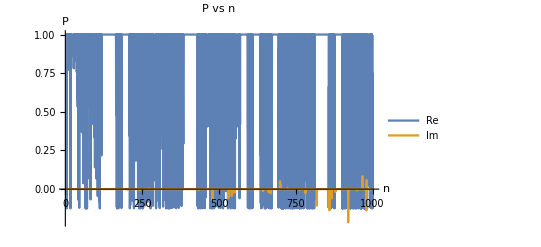

```mathematica
Plot[{Re[P],Im[P]}, {n,1,10^3}, AxesLabel->{"n", "P"},PlotLegends->{"Re", "Im"},  PlotLabel->"P vs n"]
```

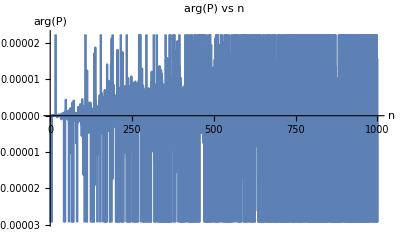

```mathematica
Plot[Arg[P], {n,1,10^3}, AxesLabel->{"n", "arg(P)"},  PlotLabel->"arg(P) vs n"]
```

# Fock ED

```mathematica
Clear[a, q, θ]
```

```mathematica
d1F =FullSimplify[ -V0/3(Subscript[k, F]^2/(8 (1 + κ^2)))(8 π + κ^2 (8 π - 3 I a n q (Sqrt[3] Cos[θ] + 3 Sin[θ])))]
```

(π V0 (-9 a^2-16 π^2+6 ⅈ a n π q (√3 Cos[θ]+3 Sin[θ])))/(30000 (9 a^2+16 π^2))

```mathematica
d2F = FullSimplify[(-V0/3) (Subscript[k, F]^2/4) (4 π + (3 Sqrt[3] I a n κ^2 q Cos[θ])/(1 + κ^2))]
```

-(π V0 (9 a^2+16 π^2+12 ⅈ √3 a n π q Cos[θ]))/(30000 (9 a^2+16 π^2))

```mathematica
d3F = FullSimplify[(-V0/3) (Subscript[k, F]^2/(8 (1 + κ^2))) (8 π + κ^2 (8 π + 3 I a n q (Sqrt[3] Cos[θ] - 3 Sin[θ])))]
```

-(π V0 (9 a^2+16 π^2+6 ⅈ a n π q (√3 Cos[θ]-3 Sin[θ])))/(30000 (9 a^2+16 π^2))

```mathematica
HF = FullSimplify[{{0, d1F, Conjugate[d3F]}, {Conjugate[d1F], 0, d2F}, {d3F, Conjugate[d2F] ,0}}]
```

{{0,(π V0 (-9 a^2-16 π^2+6 ⅈ a n π q (√3 Cos[θ]+3 Sin[θ])))/(30000 (9 a^2+16 π^2)),-(π V0 (9 a^2+16 π^2-6 ⅈ a n π q (√3 Cos[Conjugate[θ]]-3 Sin[Conjugate[θ]])))/(30000 (9 a^2+16 π^2))},{-(π V0 (9 a^2+16 π^2+6 ⅈ a n π q (√3 Cos[Conjugate[θ]]+3 Sin[Conjugate[θ]])))/(30000 (9 a^2+16 π^2)),0,-(π V0 (9 a^2+16 π^2+12 ⅈ √3 a n π q Cos[θ]))/(30000 (9 a^2+16 π^2))},{-(π V0 (9 a^2+16 π^2+6 ⅈ a n π q (√3 Cos[θ]-3 Sin[θ])))/(30000 (9 a^2+16 π^2)),-(π V0 (9 a^2+16 π^2-12 ⅈ √3 a n π q Cos[Conjugate[θ]]))/(30000 (9 a^2+16 π^2)),0}}

```mathematica
q = 10^-7
a = 1
V0 = 1
Subscript[k, F] = 10^-2
```

1/10000000

1

1

1/100

```mathematica
θ = 0
```

0

```mathematica
v0p1 = Normalize[First[Eigenvectors[HF]]]
```

{-(((45000000-3 ⅈ √3 n π+80000000 π^2) (45000000+6 ⅈ √3 n π+80000000 π^2-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]))/(√(1+Abs[((45000000-3 ⅈ √3 n π+80000000 π^2) (45000000+6 ⅈ √3 n π+80000000 π^2-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]))/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2+Abs[(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-6 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2) (2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2))),-((2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-6 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(√(1+Abs[((45000000-3 ⅈ √3 n π+80000000 π^2) (45000000+6 ⅈ √3 n π+80000000 π^2-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]))/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2+Abs[(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-6 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2) (2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2))),1/(√(1+Abs[((45000000-3 ⅈ √3 n π+80000000 π^2) (45000000+6 ⅈ √3 n π+80000000 π^2-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]))/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2+Abs[(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-6 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2))}

```mathematica
θ = 2 π/3
```

(2 π)/3

```mathematica
v0p3 = Normalize[First[Eigenvectors[HF]]]
```

{-((2025000000000000-270000000 ⅈ √3 n π+7200000000000000 π^2-27 n^2 π^2-480000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-6 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(√(1+Abs[(2025000000000000+405000000 ⅈ √3 n π+7200000000000000 π^2-54 n^2 π^2+720000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2+Abs[(2025000000000000-270000000 ⅈ √3 n π+7200000000000000 π^2-27 n^2 π^2-480000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-6 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2) (2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2))),-((2025000000000000+405000000 ⅈ √3 n π+7200000000000000 π^2-54 n^2 π^2+720000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(√(1+Abs[(2025000000000000+405000000 ⅈ √3 n π+7200000000000000 π^2-54 n^2 π^2+720000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2+Abs[(2025000000000000-270000000 ⅈ √3 n π+7200000000000000 π^2-27 n^2 π^2-480000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-6 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2) (2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2))),1/(√(1+Abs[(2025000000000000+405000000 ⅈ √3 n π+7200000000000000 π^2-54 n^2 π^2+720000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2+Abs[(2025000000000000-270000000 ⅈ √3 n π+7200000000000000 π^2-27 n^2 π^2-480000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-6 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+27 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2-12150000000 n^2 π^2+1728000000000000000000000 π^4-21600000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2))}

```mathematica
θ = 4 π/3
```

(4 π)/3

```mathematica
v0p5 = Normalize[First[Eigenvectors[HF]]]
```

{-((2025000000000000+135000000 ⅈ √3 n π+7200000000000000 π^2+54 n^2 π^2+240000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(√(1+Abs[(2025000000000000+135000000 ⅈ √3 n π+7200000000000000 π^2+54 n^2 π^2+240000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+108 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2+Abs[(2025000000000000-405000000 ⅈ √3 n π+7200000000000000 π^2-54 n^2 π^2-720000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+108 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2) (2025000000000000+7200000000000000 π^2+108 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2))),-((2025000000000000-405000000 ⅈ √3 n π+7200000000000000 π^2-54 n^2 π^2-720000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(√(1+Abs[(2025000000000000+135000000 ⅈ √3 n π+7200000000000000 π^2+54 n^2 π^2+240000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+108 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2+Abs[(2025000000000000-405000000 ⅈ √3 n π+7200000000000000 π^2-54 n^2 π^2-720000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+108 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2) (2025000000000000+7200000000000000 π^2+108 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2))),1/(√(1+Abs[(2025000000000000+135000000 ⅈ √3 n π+7200000000000000 π^2+54 n^2 π^2+240000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+108 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2+Abs[(2025000000000000-405000000 ⅈ √3 n π+7200000000000000 π^2-54 n^2 π^2-720000000 ⅈ √3 n π^3+6400000000000000 π^4-45000000 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]+3 ⅈ √3 n π Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]-80000000 π^2 Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1])/(2025000000000000+7200000000000000 π^2+108 n^2 π^2+6400000000000000 π^4-Root[182250000000000000000000+972000000000000000000000 π^2+2430000000 n^2 π^2+1728000000000000000000000 π^4+4320000000 n^2 π^4+1024000000000000000000000 π^6+(-6075000000000000-21600000000000000 π^2-162 n^2 π^2-19200000000000000 π^4) #1+#1^3&,1]^2)]^2))}

```mathematica
P = (Conjugate[v0p1].v0p3) * (Conjugate[v0p3].v0p5) * (Conjugate[v0p5].v0p1)
```

(Conjugate[1/(√(1+Abs[1]^2+Abs[1]^2))]/(√(1+Abs[1/1]^2+Abs[1/1]^2))+1/1+((45000000+80000000 π^2+3 ⅈ √3 π Conjugate[n]) Conjugate[1/1] 1 (1))/(√(1+Abs[1]^2+Abs[1/1]^2) (1) (1))) 1 (1)
 |  |  |  |

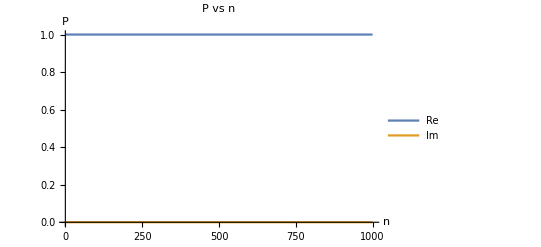

```mathematica
Plot[{Re[P],Im[P]}, {n,1,10^3}, AxesLabel->{"n", "P"},PlotLegends->{"Re", "Im"},  PlotLabel->"P vs n"]
```

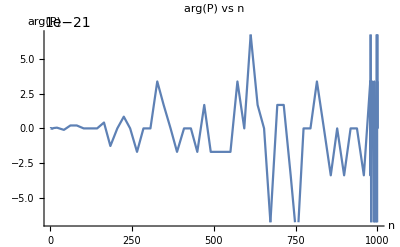

```mathematica
Plot[Arg[P], {n,1,10^3}, AxesLabel->{"n", "arg(P)"},  PlotLabel->"arg(P) vs n"]
```

# Fock Berry Curvature